The black points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.

{0.,0.0238549,0.0486817,0.0665656,0.0736202,0.0744135,0.0786365,0.0840042,0.107231,0.127008,0.14444,0.167435,0.189318,0.203811,0.21232,0.213487,0.215144,0.2246,0.238947,0.261131,0.276025,0.302449,0.317278,0.331533,0.337535,0.338733,0.341168,0.348003,0.359718,0.377026,0.39431,0.413589,0.428587,0.445287,0.454462,0.45786,0.458701,0.467856,0.482995,0.492105,0.511516,0.526877,0.541982,0.55185,0.564168,0.564972,0.572604,0.573603,0.590183,0.605593,0.61853,0.628919,0.646455,0.653539,0.661947,0.66277,0.665204,0.669695,0.683108,0.694905,0.711387,0.721859,0.736056,0.739028,0.745215,0.749487,0.75451,0.760122,0.766144,0.77636,0.79235,0.801357,0.811828,0.823859,0.830574,0.835754,0.838067,0.848374,0.851941,0.860665,0.875723,0.888541,0.898128,0.904915,0.906683,0.907939,0.910082,0.919691,0.921614,0.935369,0.939503,0.956179,0.964069,0.968328,0.971774,0.973326,0.974609,0.98157,0.987684,0.995985,1.}

{0,0,0,0,1/15,2/15,1/5,4/15,1/3,2/5,7/15,8/15,3/5,2/3,11/15,4/5,13/15,14/15,1,1,1,1}

{0,0,0,0,0.076525,0.196564,0.268578,0.33995,0.436937,0.50181,0.573103,0.649997,0.703146,0.757316,0.827217,0.868194,0.914886,0.970051,1,1,1,1}

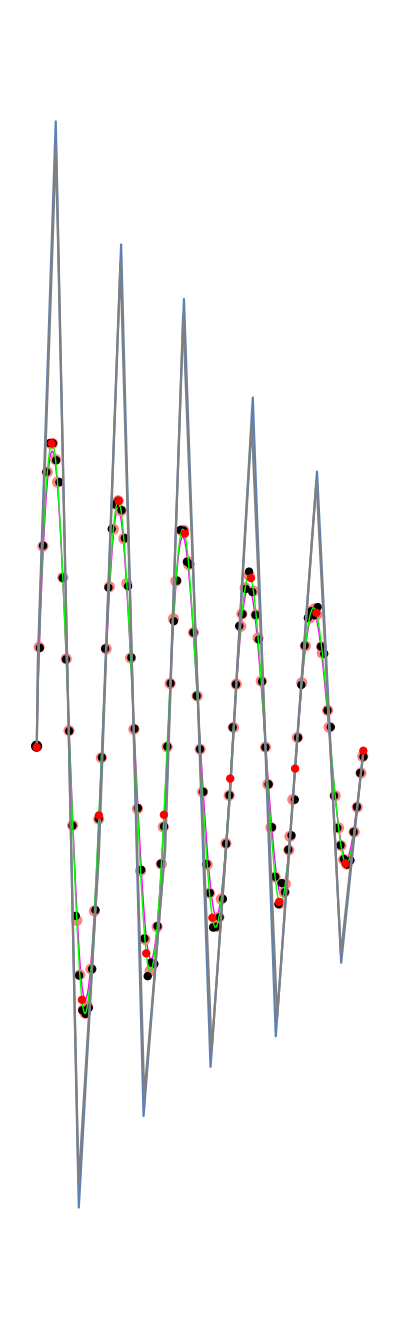

| Max | Min | Ave
1st iter err | 0.123747 | 0.00376758 | 0.0444521
Last iter err | 0.0208032 | 0.000440008 | 0.00409565

| Max | Min | Ave
1st iter ang | 3.14072 | 0.00296524 | 1.56961
Last iter ang | 2.9774 | 0.0787663 | 1.61146

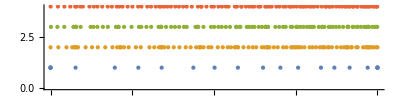

```mathematica
(*data4 contaions 100 points. I didn't add it to manipulate since it is too slow. I show it in another file.*)
data1=Table[{Cos[x]//N, Sin[x]//N},{x,0,6}];
data2=Table[{x, Sin[x]//N},{x,0,12}];
data3=Table[{x,x},{x,1,10}];
data4=Table[{i,Exp[-i]Sin[10Pi i]+RandomReal[.1]},{i,0,1,.01}];

(*d is degree,which is three,n is # of control point*)

l=15;
iter=6;


(*chord length parameter*)
(*calculate the distance for parameter*)
dist[pts_]:=Accumulate[Table[EuclideanDistance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}]];
(*set ti from 0 to 1 by using Chord length*)
uparam[pts_]:=N[Prepend[dist[pts]/Last[dist[pts]],0]];

(*I used the two function to calculate the knots first. The result is almost the same, so I used uniformed knots.*)
(*set ti for different control points*)
ctrlparam[n_,pts_,param_]:=Join[Table[0,{i,0,0}],Table[Sum[param[[i]],{i,j,Length[pts]-n+j}]/(Length[pts]-n+1),{j,2,n-1}],Table[1,{i,0,0}]];
(*set knot for different degree*)
kfun[d_,ctrlparam_]:=Join[Table[0,{i,0,d}],Table[Sum[ctrlparam[[i]],{i,j,j+d-1}]/d,{j,2,Length[ctrlparam]-d}], Table[1,{i,0,d}]];

knotfun[l_,uparam_]:=Join[Table[0,{i,0,3}],Table[(uparam[[Ceiling[i*Length[uparam]/l]]]+uparam[[Floor[i*Length[uparam]/l]]])/2,{i,1,l-1}],Table[1,{i,0,3}]];
(*calculate the basis*)
(*Built the matrix M for least square*)
mbasis[uparam_,n_,d_,knot_]:=With[{param=uparam},Table[BSplineBasis[{d,knot},j-1,param[[i]]],{i,Length[param]},{j,n}]];
curve[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];



Print[Style["The black points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.",18,Red]];
pts=data4;

n=l+3;
d=3;

(*Original parameter.*)
param=uparam[pts]
(*(*For different amount of control points, set different parameter.*)
ctrlparameter=ctrlparam[n,pts,param];*)
(*The knots for different degree*)

knot=Join[ConstantArray[0,d],Range[0,1,1/(n-d)],ConstantArray[1,d]]
knot=knotfun[l,param]
(*The control point*)
ctrlpts=LeastSquares[mbasis[param,n,d,knot],pts];
mbasis[param,n,d,knot];

crtparam=param;
(*crtctrlparameter=ctrlparameter;*)
crtknot=knot;
crtctrlpts=ctrlpts;
(*use this funtion to get the vector on curve*)
divcurve[t_]:=curve[crtctrlpts,crtknot,n,d,t];

(*The length of the curve.*)
curvelength=ArcLength[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],knot[[Length[crtknot]-d]]}];

(*error represent the distance between original data points with the points on the curve which set by parameter ti.*)
error=Table[0,{j,1,Length[pts]}];
(*The vector at ti on the curve*)
tengentvec=Table[{0,0},{j,1,Length[pts]}];
(*The vecter from points on curve to data points*)
errvec=Table[{0,0},{j,1,Length[pts]}];
(*The angle between two vecter*)
vecang=Table[0,{j,1,Length[pts]}];
(*The length used to change ti*)
lengthl=Table[0,{j,1,Length[pts]}];
error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;

Do[(
Do[
error[[j]]=EuclideanDistance[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],pts[[j]]];
tengentvec[[j]]=divcurve'[crtparam[[j]]];
errvec[[j]]=pts[[j]]-curve[crtctrlpts,crtknot,n,d,crtparam[[j]]];
If[error[[j]]==0,vecang[[j]]=0,vecang[[j]]=VectorAngle[tengentvec[[j]],errvec[[j]]]];
lengthl[[j]]=error[[j]]*Cos[vecang[[j]]];
(*Parameter correction. If the length of new vector is less than the original vector, do the correction, else the ti will be corrected by half of the length.*)
tmplengthl=lengthl[[j]];
tmpparam=crtparam[[j]];
If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];
While[EuclideanDistance[curve[crtctrlpts,crtknot,n,d,tmpparam],pts[[j]]]>error[[j]]&&tmplengthl≠0,(tmplengthl=tmplengthl/2;If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];)];
If[tmpparam<0,crtparam[[j]]=0,If[tmpparam>1,crtparam[[j]]=1,crtparam[[j]]=tmpparam;]];
,{j,1,Length[pts]}];
(*Here is the control points after correction*)
crtctrlpts=LeastSquares[mbasis[crtparam,n,d,crtknot],pts];
(*store the data after first iteration*)
If[k==1,
(error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;
crtparam1=crtparam;)];

)
,{k,1,iter}];

(*get the max, min, mean error and angle*)
errmax1=Max[error1];
errmin1=Min[error1];
errave1=Mean[error1];
errmax=Max[error];
errmin=Min[error];
errave=Mean[error];
angmax1=Max[vecang1];
angmin1=Min[vecang1];
angave1=Mean[vecang1];
angmax=Max[vecang];
angmin=Min[vecang];
angave=Mean[vecang];

(*Output the curves, points and polygon*)
datapts=Graphics[{Black,PointSize[0.015],Point[pts],PointSize[0.02],Point[pts[[1]]]}];
jpts = Table[curve[crtctrlpts,crtknot,n,d,crtknot[[i]]], {i,d+1,Length[crtknot]- d,1}];
jptsplot = Graphics[{Red,PointSize[0.015],Point[jpts]}];
parpts=Table[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],{j,1,Length[pts]}];
parptsplot=Graphics[{Pink,PointSize[0.02],Point[parpts]}];
ctrlpoints=Graphics[{Green,PointSize[0.015],Point[crtctrlpts],PointSize[0.02],Point[crtctrlpts[[1]]]}];
cplot=ParametricPlot[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Green}];
cplot1=ParametricPlot[curve[crtctrlpts1,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Magenta}];
ddplot=ListLinePlot[crtctrlpts];
ddplot1=ListLinePlot[crtctrlpts1,PlotStyle->Gray];

Show[{cplot1,parptsplot,datapts,cplot,ddplot,ddplot1,jptsplot},Axes->False,PlotRange->All,ImageSize->400]
TableForm[{{errmax1,errmin1,errave1},{errmax,errmin,errave}},TableHeadings->{{"1st iter err","Last iter err"},{"Max","Min","Ave"}},TableDirections->Column]
TableForm[{{angmax1,angmin1,angave1},{angmax,angmin,angave}},TableHeadings->{{"1st iter ang","Last iter ang"},{"Max","Min","Ave"}},TableDirections->Column]
NumberLinePlot[{crtknot,param,crtparam1,crtparam}]
```